```mathematica
N@Sin[3I+Pi/2]
```

10.0677

```mathematica
N@Cos[3I]
```

10.0677

```mathematica
bra7b[n_,x_]:=Sum[ (1/j)^(1/2)(2 x Cos[ x Log[n/j]]-Sin[x Log[n/j]]),{j,1,n}]
bra7c[n_,x_]:=((2 x Sin[ x Log[n]]+Cos[x Log[n]])Sum[ (j)^(-1/2)Sin[x Log[j]],{j,1,n}]+(2 x Cos[ x Log[n]]-Sin[x Log[n]])Sum[ (j)^(-1/2)Cos[x Log[j]],{j,1,n}])
bra8c[n_,x_]:=(( x Sin[ x Log[n]]+(1/2)Cos[x Log[n]])/( x Cos[ x Log[n]]-(1/2)Sin[x Log[n]])Sum[ j^(-1/2)Sin[x Log[j]],{j,1,n}]+Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}])
bra8d[n_,x_]:=Tan[x Log[n]+ArcCot[2 x]]Sum[ j^(-1/2)Sin[x Log[j]],{j,1,n}]+Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]
bra8e[n_,x_]:=Sum[ j^(-1/2)(Tan[x Log[n]+ArcCot[2 x]]Sin[x Log[j]]+Cos[x Log[j]]),{j,1,n}]
bra8ex[n_,x_]:=Sum[ j^(-1/2)(Sin[x Log[j]]+Cos[x Log[j]]),{j,1,n}]
fs[n_,x_]:=Tan[x Log[n]+ArcCot[2 x]]
```

```mathematica
bra8e[10000,.9I-.5I+ 30]
```

0.344309+0.503637 ⅈ

```mathematica
Zeta[30I+.9]
```

0.344439-0.503704 ⅈ

```mathematica
Sin[x]/Cos[x]
```

Tan[x]

```mathematica
Cos[x]/-Sin[x]
```

-Cot[x]

```mathematica
ArcCot[2 N@Im@ZetaZero@1]
```

0.0353591

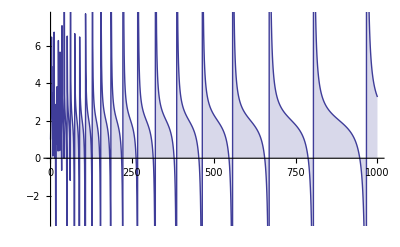

```mathematica
DiscretePlot[Re@bra8e[n,N@Im@ZetaZero@1+3],{n,1,1000}]
```

```mathematica
fs[n,N@Im@ZetaZero@3]
```

Tan[0.0199887+25.0109 Log[n]]

```mathematica
bra8es[n_,x_]:={Tan[x Log[n]+ArcCot[2 x]],Sum[ j^(-1/2)(Sin[x Log[j]]),{j,1,n}],Sum[ j^(-1/2)(Cos[x Log[j]]),{j,1,n}]}
```

```mathematica
bra8es[1000,3I-.5I+1000]
```

{-1.8733×10^-15+1. ⅈ,426052.-69231.6 ⅈ,-69230.7-426052. ⅈ}

```mathematica
sl[n_,s_]:=Sum[((1-s)/s)^(1/2)(n/j)^s- ((1-s)/s)^(-1/2) (n/j)^(1-s),{j,1,n}]
sl3[n_,s_]:=Sum[((1-(s+1/2))/(s+1/2))^(1/2)(n/j)^(s+1/2)- ((1-(s+1/2))/(s+1/2))^(-1/2) (n/j)^(1-(s+1/2)),{j,1,n}]
sl4[n_,s_]:=Sum[((1/2-s)/(s+1/2))^(1/2)(n/j)^(1/2+s)- ((1/2-s)/(s+1/2))^(-1/2) (n/j)^(1/2-s),{j,1,n}]
sl5[n_,s_]:=Sum[(n/j)^(1/2)(((1/2-s)/(s+1/2))^(1/2)(n/j)^s- ((1/2-s)/(s+1/2))^(-1/2) (n/j)^-s),{j,1,n}]
sl6[n_,s_]:=Sum[(n/j)^(1/2)(((1/2-s)/(s+1/2))^(1/2)(n/j)^s- (((1/2-s)/(s+1/2))^(1/2) (n/j)^s)^-1),{j,1,n}]
```

```mathematica
sl6[100000,N@ZetaZero@10-.5]
```

7.59762×10^-14-0.99995 ⅈ

```mathematica
(1/2-s)/(1/2+s)
```

(1/2-s)/(1/2+s)

```mathematica
((1-(s+1/2))/(s+1/2))
```

(1/2-s)/(1/2+s)

```mathematica
FullSimplify[a^1-a^-1]
```

-1/a+a

```mathematica
Expand[(((1/2-s)/(s+1/2))^(1/2)(n/j)^s- (((1/2-s)/(s+1/2))^(1/2) (n/j)^s)^-1)]
```

(n/j)^s √((1/2-s)/(1/2+s))-((n/j)^-s √((1/2-s)/(1/2+s)))/(2 (1/2-s))-((n/j)^-s s √((1/2-s)/(1/2+s)))/(1/2-s)

```mathematica
FullSimplify[(1/2-t I)/(1/2+t I)^(1/2) - (1/2-t I)/(1/2+t I)^(-1/2)]
```

-(ⅈ+2 t)^2/(2 √(2+4 ⅈ t))

```mathematica
-(ⅈ+2 t)^2/(2 √(2+4 ⅈ t))/.t->N@Im@ZetaZero@1
```

-40.7853+34.1444 ⅈ

```mathematica
FullSimplify[(1/2-t I)/(1/2+t I)^(1/2) + (1/2-t I)/(1/2+t I)^(-1/2)]
```

```mathematica
(3+4 t (-ⅈ+t))/(2 √(2+4 ⅈ t))/.t->N@Im@ZetaZero@1
```

35.7562-39.7375 ⅈ

```mathematica
sl7[n_,s_]:=Sum[j^(-1/2)(((1/2-s)/(s+1/2))^(1/2)(n/j)^s- (((1/2-s)/(s+1/2))^(1/2) (n/j)^s)^-1),{j,1,n}]
sl8[n_,s_,t_]:=Sum[j^(-1/2)(((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^(s+t I)- (((1/2-s-t I)/(s+t I+1/2))^(1/2) (n/j)^(s+t I))^-1),{j,1,n}]
sl9[n_,s_,t_]:=Sum[j^(-1/2)(((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s(n/j)^(t I)- (((1/2-s-t I)/(s+t I+1/2))^(-1/2) (n/j)^(-s)(n/j)^(-t I))),{j,1,n}]
sl10[n_,s_,t_]:=Sum[j^(-1/2)(((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s(Cos[t Log[n/j]]+I Sin[t Log[n/j]])- (((1/2-s-t I)/(s+t I+1/2))^(-1/2) (n/j)^(-s)(Cos[t Log[n/j]]-I Sin[t Log[n/j]]))),{j,1,n}]
sl11[n_,s_,t_]:=Sum[j^(-1/2)(((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s(Cos[t Log[n/j]])- (((1/2-s-t I)/(s+t I+1/2))^(-1/2) (n/j)^(-s)(Cos[t Log[n/j]]))),{j,1,n}]+Sum[j^(-1/2)(((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s(I Sin[t Log[n/j]])- (((1/2-s-t I)/(s+t I+1/2))^(-1/2) (n/j)^(-s)(-I Sin[t Log[n/j]]))),{j,1,n}]
ov[s_,t_]:=((1/2-s-t I)/(s+t I+1/2))^(1/2)
ot[s_,t_,n_,j_]:=((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s
sl12[n_,s_,t_]:=Sum[j^(-1/2)(ov[s,t](n/j)^s(Cos[t Log[n/j]])- (1/ov[s,t] (n/j)^-s(Cos[t Log[n/j]]))),{j,1,n}]+Sum[j^(-1/2)(ov[s,t](n/j)^s(I Sin[t Log[n/j]])- (1/ov[s,t] (n/j)^(-s)(-I Sin[t Log[n/j]]))),{j,1,n}]
sl13[n_,s_,t_]:=Sum[j^(-1/2)(ot[s,t,n,j](Cos[t Log[n/j]])- (1/ot[s,t,n,j](Cos[t Log[n/j]]))),{j,1,n}]+Sum[j^(-1/2)(ot[s,t,n,j](I Sin[t Log[n/j]])- (1/ot[s,t,n,j](-I Sin[t Log[n/j]]))),{j,1,n}]
sl14[n_,s_,t_]:=Sum[j^(-1/2)(ot[s,t,n,j]Cos[t Log[n/j]]- (1/ot[s,t,n,j]Cos[t Log[n/j]])),{j,1,n}]+I Sum[j^(-1/2)(ot[s,t,n,j] Sin[t Log[n/j]]+ (1/ot[s,t,n,j] Sin[t Log[n/j]])),{j,1,n}]
sl15[n_,s_,t_]:=Sum[j^(-1/2)((ot[s,t,n,j]- 1/ot[s,t,n,j])Cos[t Log[n/j]]),{j,1,n}]+I Sum[j^(-1/2)((ot[s,t,n,j] + 1/ot[s,t,n,j]) Sin[t Log[n/j]]),{j,1,n}]
sl16[n_,s_,t_]:=Sum[j^(-1/2)((ot[s,t,n,j]- 1/ot[s,t,n,j])Cos[t Log[n/j]]+I ((ot[s,t,n,j] + 1/ot[s,t,n,j]) Sin[t Log[n/j]])),{j,1,n}]
sl16a[n_,s_,t_]:=Sum[j^(-1/2)((ot[s,t,n,j]- 1/ot[s,t,n,j])Cos[t Log[n/j]]),{j,1,n}]
sl16b[n_,s_,t_]:=Sum[j^(-1/2)(I ((ot[s,t,n,j] + 1/ot[s,t,n,j]) Sin[t Log[n/j]])),{j,1,n}]
```

```mathematica
sl16[10000,.1,N@Im@ZetaZero@4]
```

-0.0417406+0.234708 ⅈ

```mathematica
bb[s_,t_]:=(1/2-s-t I)/(1/2+s+t I)^(1/2)
bb2[s_,t_]:=(1/2-s-t I)/(1/2+s+t I)^(-1/2)
```

```mathematica
N[bb[0,30]-bb2[0,30]]
```

-120.953+111.272 ⅈ

```mathematica
N@2^(1/12)
```

1.05946

```mathematica
bo[n_,s_]:=( n^(1-s))/((1-s)n^s HarmonicNumber[n,s]-s n^(1-s)HarmonicNumber[n,1-s])
```

```mathematica
bo[10000000,.7]
```

-0.00190374

```mathematica
Zeta[.7]
```

-2.77839

```mathematica
((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s/.s->0/.t->N@Im@ZetaZero@1
```

0.0353518-0.999375 ⅈ

```mathematica
ot[0,N@Im@ZetaZero@1,1,1000]-1/ot[0,N@Im@ZetaZero@1,1,1000]
```

0.-1.99875 ⅈ

```mathematica
N[Pi/2]
```

1.5708

```mathematica
FullSimplify[((1/2+s+t I)/(1/2-s-t I))^(-1/2)]
```

1/(√(-1+2/(1-2 s-2 ⅈ t)))

```mathematica
ot[s_,t_,n_,j_]:=((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s
oxa[s_,t_,n_,j_]:=(n/j)^s √(-1+2/(1+2 s+2 ⅈ t))
ox[s_,t_,n_,j_]:=(n/j)^s √(-1+(2(1+2s - 2 I t))/((1+2 s)^2+4 t^2))
sl16[n_,s_,t_]:=Sum[j^(-1/2)((ot[s,t,n,j]- 1/ot[s,t,n,j])Cos[t Log[n/j]]+I ((ot[s,t,n,j] + 1/ot[s,t,n,j]) Sin[t Log[n/j]])),{j,1,n}]
sl17[n_,s_,t_]:=Sum[j^(-1/2)((ox[s,t,n,j]- 1/ox[s,t,n,j])Cos[t Log[n/j]]+I ((ox[s,t,n,j] + 1/ox[s,t,n,j]) Sin[t Log[n/j]])),{j,1,n}]
```

```mathematica
sl17[10000,0,N@Im@ZetaZero@4]
```

0.-0.00999865 ⅈ

```mathematica
sl16[10000,0,N@Im@ZetaZero@4]
```

-3.64808×10^-16-0.00999865 ⅈ

```mathematica
FullSimplify[((1/2-s-t I)/(s+t I+1/2))^(1/2)(n/j)^s]
```

(n/j)^s √(-1+2/(1+2 s+2 ⅈ t))

```mathematica
FullSimplify[Expand[(1+2s+2I t)(1+2s - 2 I t)]]
```

(1+2 s)^2+4 t^2

```mathematica
FullSimplify[(n/j)^s √(-1+(2(1+2s - 2 I t))/((1+2 s)^2+4 t^2))]
```

(n/j)^s √(-1+2/(1+2 s+2 ⅈ t))

```mathematica
FullSimplify[2(1+2s - 2 I t)]
```

2+4 s-4 ⅈ t

```mathematica
pl[n_,x_]:=Sum[ j^(-1/2)(Cos[x Log[n]+ArcCot[2x]]Cos[x Log[j]]+Sin[x Log[n]+ArcCot[2x]]Sin[x Log[j]]),{j,1,n}]
plb[n_,x_]:=Sum[ j^(-1/2)(Cos[x Log[j]]+Tan[x Log[n]+ArcCot[2x]]Sin[x Log[j]]),{j,1,n}]
plc[n_,x_]:=Sum[ j^(-1/2)(Cos[x Log[n]+ArcCot[2x]]Cos[x Log[j]]+Sin[x Log[n]+ArcCot[2x]]Sin[x Log[j]]),{j,1,n}]
pld[n_,x_]:=Cos[x Log[n]+ArcCot[2x]]Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]+Sin[x Log[n]+ArcCot[2x]]Sum[ j^(-1/2)Sin[x Log[j]],{j,1,n}]
pldr[n_,x_,c_]:=Cos[x Log[n]+ArcCot[2x]+c]Sum[ j^(-1/2)Cos[x Log[j]+c],{j,1,n}]+Sin[x Log[n]+ArcCot[2x]+c]Sum[ j^(-1/2)Sin[x Log[j]+c],{j,1,n}]
pldx[n_,x_]:=(1/2)(E^(I(x Log[n]+ArcCot[2x]))+E^(-I(x Log[n]+ArcCot[2x])))Sum[ j^(-1/2)((1/2)(E^(I(x Log[j]))+E^(-I(x Log[j])))),{j,1,n}]+Sin[x Log[n]+ArcCot[2x]]Sum[ j^(-1/2)Sin[x Log[j]],{j,1,n}]
pldx2[n_,x_]:=Sum[ j^(-1/2)(1/2)(E^(I(x Log[n]+ArcCot[2x]))+E^(-I(x Log[n]+ArcCot[2x])))((1/2)(E^(I(x Log[j]))+E^(-I(x Log[j])))),{j,1,n}]+Sin[x Log[n]+ArcCot[2x]]Sum[ j^(-1/2)Sin[x Log[j]],{j,1,n}]
pldr2[n_,x_,c_,d_]:=Cos[x Log[n]+ArcCot[2x]+c]Sum[ j^(-1/2)Cos[x Log[j]+c],{j,1,n}]+Sin[x Log[n]+ArcCot[2x]+d]Sum[ j^(-1/2)Sin[x Log[j]+d],{j,1,n}]
pldr2a[n_,x_,c_,d_]:=Cos[x Log[n]+ArcCot[2x]+c]Sum[ j^(-1/2)Cos[x Log[j]+c],{j,1,n}]
pldr2b[n_,x_,c_,d_]:=Sin[x Log[n]+ArcCot[2x]+d]Sum[ j^(-1/2)Sin[x Log[j]+d],{j,1,n}]
```

```mathematica
pldr2[10000,N@Im@ZetaZero@10,Pi/2,0]
```

0.887172

```mathematica
Cos[x Log[n]+ArcCot[2x]]Sum[ j^(-1/2)Cos[x Log[j]],{j,1,n}]+Sin[x Log[n]+ArcCot[2x]]Sum[ j^(-1/2)Sin[x Log[j]],{j,1,n}]
```

Cos[ArcCot[2 x]+x Log[n]] ∑_(j=1)^n Cos[x Log[j]]/(√j)+Sin[ArcCot[2 x]+x Log[n]] ∑_(j=1)^n Sin[x Log[j]]/(√j)

```mathematica
FullSimplify[j^(-1/2)(1/2)(E^(I(x Log[n]+ArcCot[2x]))+E^(-I(x Log[n]+ArcCot[2x])))((1/2)(E^(I(x Log[j]))+E^(-I(x Log[j]))))]
```

1/2 j^(-1/2-ⅈ x) (1+j^(2 ⅈ x)) Cos[ArcCot[2 x]+x Log[n]]

```mathematica
plc[n_,x_]:=Sum[ j^(-1/2)(Cos[x Log[n]+ArcCot[2x]]Cos[x Log[j]]+Sin[x Log[n]+ArcCot[2x]]Sin[x Log[j]]),{j,1,n}]
plc2[n_,x_]:=Sum[ j^(-1/2)((1/2)(Cos[x Log[n]+ArcCot[2x]+x Log[j]]+Cos[x Log[n]+ArcCot[2x]-x Log[j]])+Sin[x Log[n]+ArcCot[2x]]Sin[x Log[j]]),{j,1,n}]
plc3[n_,x_]:=Sum[ j^(-1/2)((1/2)(Cos[x Log[n]+ArcCot[2x]+x Log[j]]+Cos[x Log[n]+ArcCot[2x]-x Log[j]])+((1/2)(Cos[x Log[n]+ArcCot[2x]-x Log[j]]-Cos[x Log[n]+ArcCot[2x]+x Log[j]]))),{j,1,n}]
plc4[n_,x_]:=Sum[ j^(-1/2)Cos[ArcCot[2 x]+x (-Log[j]+Log[n])],{j,1,n}]
plc5[n_,x_]:=Sum[Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2),{j,1,n}]
plc5a[n_,x_]:=(1/Cos[ArcCot[2 x]+x  Log[n]])Sum[Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2),{j,1,n}]
```

```mathematica
plc5a[1000000,N@Im@ZetaZero@20]
```

-0.000719073

```mathematica
plc5[1000000,N@Im@ZetaZero@20]
```

0.000499989

```mathematica
FullSimplify[((1/2)(Cos[x Log[n]+ArcCot[2x]+x Log[j]]+Cos[x Log[n]+ArcCot[2x]-x Log[j]])+((1/2)(Cos[x Log[n]+ArcCot[2x]-x Log[j]]-Cos[x Log[n]+ArcCot[2x]+x Log[j]])))]
```

Cos[ArcCot[2 x]+x (-Log[j]+Log[n])]

```mathematica
Zeta[.8+10I]
```

1.44628-0.113501 ⅈ

```mathematica
plc5a[1000000,.2I+20]
```

0.554102+0.874923 ⅈ

```mathematica
Zeta[.7+20I]
```

0.557271-0.882999 ⅈ

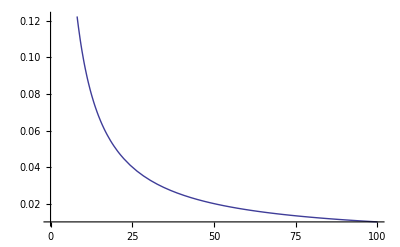

```mathematica
Plot[Abs@ArcCot[n],{n,0,100}]
```

```mathematica
ArcCot[0]
```

π/2

```mathematica
plc5a[100000,1.5I]
```

1.64493+0. ⅈ

```mathematica
FullSimplify[(1/Cos[ArcCot[2 x]+x  Log[n]])Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2)/.x->3/2I]
```

(Cosh[ArcCoth[3]-3/2 Log[n/j]] Sech[ArcCoth[3]-(3 Log[n])/2])/(√j)

```mathematica
Sum[(Cosh[ArcCoth[3]-3/2 Log[n/j]] Sech[ArcCoth[3]-(3 Log[n])/2])/(√j),{j,1,n}]
```

∑_(j=1)^n (Cosh[ArcCoth[3]-3/2 Log[n/j]] Sech[ArcCoth[3]-(3 Log[n])/2])/(√j)

```mathematica
plc5b[n_,x_]:=Sum[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
plc5c[n_,x_]:=Table[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
plc5d[n_,x_]:=DiscretePlot[{Re[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]]],Im[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]]]},{j,1,n}]
plc5d2[n_,x_]:=DiscretePlot[{Re[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))],Im[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))]},{j,1,n}]
```

```mathematica
plc5[n_,x_]:=Sum[Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2),{j,1,n}]
plc5w[n_,x_]:=Sum[Cos[ArcCot[2 x]+x  Log[n/j]](n/j)^(1/2),{j,1,n}]
plc5x[n_,x_]:=Sum[((1/2)(E^(I(x  Log[n/j]+ArcCot[2 x]))+E^(-I(x  Log[n/j]+ArcCot[2 x]))))/j^(1/2),{j,1,n}]
plc5y[n_,x_]:=Sum[((1/2)(E^(I(x  Log[n/j]))E^(I ArcCot[2 x])+E^(-I(x  Log[n/j]))E^(-I(ArcCot[2 x]))))/j^(1/2),{j,1,n}]
plc5z[n_,x_]:=Sum[((n/j)^(1/2))((1/2)(E^(I(x  Log[n/j]))E^(I ArcCot[2 x])+E^(-I(x  Log[n/j]))E^(-I(ArcCot[2 x])))),{j,1,n}]
plc5z[n_,x_]:=Sum[((n/j)^(1/2))((1/2)(E^(I(x  Log[n/j]))E^(I ArcCot[2 x])+E^(-I(x  Log[n/j]))E^(-I(ArcCot[2 x])))),{j,1,n}]
plc5z2[n_,x_]:=Sum[1/2 ⅇ^(-ⅈ ArcCot[2 x]) (n/j)^(1/2-ⅈ x)+1/2 ⅇ^(ⅈ ArcCot[2 x]) (n/j)^(1/2+ⅈ x),{j,1,n}]
plc5z3[n_,x_]:=Sum[1/(2 n^(1/2))( ⅇ^(-ⅈ ArcCot[2 x]) (n/j)^(1/2-ⅈ x)+ⅇ^(ⅈ ArcCot[2 x]) (n/j)^(1/2+ⅈ x)),{j,1,n}]
plc5z4[n_,x_]:=Sum[1/(2 j^(1/2))( ⅇ^(-ⅈ ArcCot[2 x]) (n/j)^(-ⅈ x)+ⅇ^(ⅈ ArcCot[2 x]) (n/j)^(ⅈ x)),{j,1,n}]
plc5z5[n_,x_]:=Sum[1/(2 j^(1/2))( ⅇ^(-ⅈ ArcCot[2 x]) (n/j)^(-ⅈ x)+ⅇ^(ⅈ ArcCot[2 x]) (n/j)^(ⅈ x)),{j,1,n}]
plc5z6[n_,x_]:=Sum[1/(2 j^(1/2))( ⅇ^(-ⅈ ArcCot[2 x]) (n/j)^(-ⅈ x)),{j,1,n}]+Sum[1/(2 j^(1/2))( ⅇ^(ⅈ ArcCot[2 x]) (n/j)^(ⅈ x)),{j,1,n}]
plc5z7[n_,x_]:=(1/2)(ⅇ^(-ⅈ ArcCot[2 x])n^(-ⅈ x)Sum[(  j^(-1/2+ⅈ x)),{j,1,n}]+ⅇ^(ⅈ ArcCot[2 x]) n^(ⅈ x)Sum[ j^(-1/2-ⅈ x),{j,1,n}])
```

```mathematica
plc5z7[10000,N@Im@ZetaZero@20]
```

0.00499989+0. ⅈ

```mathematica
Expand[((n/j)^(1/2))((1/2)(E^(I(x  Log[n/j]))E^(I ArcCot[2 x])+E^(-I(x  Log[n/j]))E^(-I(ArcCot[2 x]))))]
```

1/2 ⅇ^(-ⅈ ArcCot[2 x]) (n/j)^(1/2-ⅈ x)+1/2 ⅇ^(ⅈ ArcCot[2 x]) (n/j)^(1/2+ⅈ x)

```mathematica
plc5f[n_,x_,c_]:=Sum[Cos[ArcCot[2 x]+x  Log[n]-x  Log[j]+c]/j^(1/2),{j,1,n}]
```

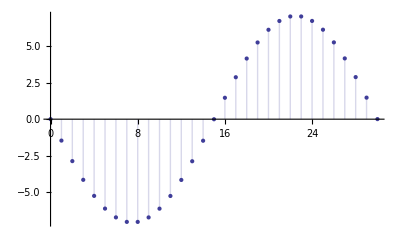

```mathematica
DiscretePlot[plc5f[10000,N@Im@ZetaZero@1,j/30*2 Pi],{j,0,30}]
```

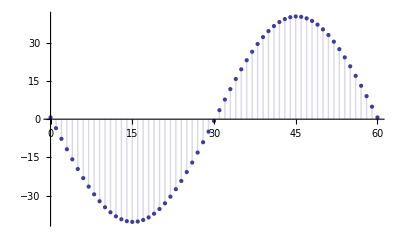

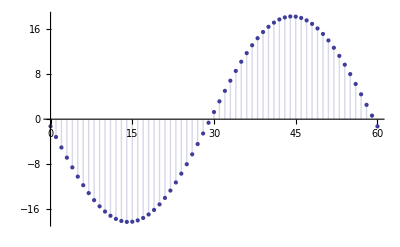

```mathematica
DiscretePlot[plc5f[30000,10,j/60*2 Pi],{j,0,60}]
```

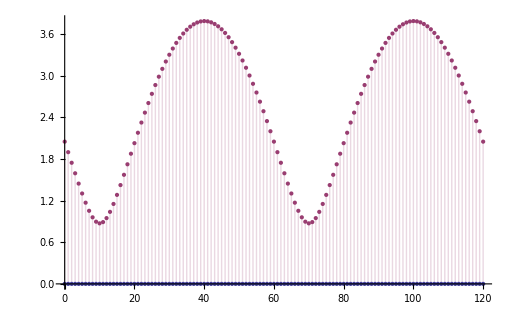

```mathematica
DiscretePlot[{0,Abs[plc5f[1000,10+.1I,j/120 * 2 Pi+.1I]]},{j,0,120}]
```

```mathematica
plc5f[2000,.1,0]
```

1.05896

```mathematica
plc5fr[n_,x_,c_]:=DiscretePlot[{Re@Cos[ArcCot[2 x]+x  Log[n]-x  Log[j]+c]/j^(1/2),Im@Cos[ArcCot[2 x]+x  Log[n]-x  Log[j]+c]/j^(1/2)},{j,1,n}]
```

```mathematica
plc5fr[10000,N@Im@ZetaZero@4+.3I,0]
```

Sum::div: Sum does not converge.

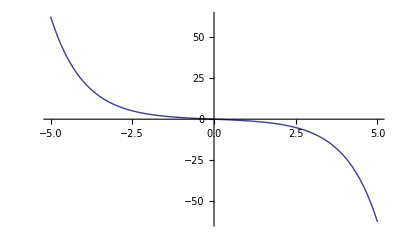

```mathematica
Plot[Im[Cos[1+x I]],{x,-5,5}]
```

```mathematica
FullSimplify[D[Cos[ArcCot[2 x]+x  Log[n]-x  Log[j]]/j^(1/2),x]]
```

-((-2/(1+4 x^2)-Log[j]+Log[n]) Sin[ArcCot[2 x]+x (-Log[j]+Log[n])])/(√j)

```mathematica
s2[n_,x_]:=Sum[-((-2/(1+4 x^2)-Log[j]+Log[n]) Sin[ArcCot[2 x]+x (-Log[j]+Log[n])])/(√j),{j,1,n}]
```

```mathematica
s2[10000,N@Im@ZetaZero@3]
```

1.34591

```mathematica
ArcCot[2 x]/.x->N@Im@ZetaZero@1
```

0.0353591

```mathematica
Cos[ArcCot[2t]]
```

1/(√(1+1/(4 t^2)))

```mathematica
plc5b[n_,x_]:=Sum[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
plc5bz[n_,x_]:=Sum[N[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]]],{j,1,n}]
```

```mathematica
plc5bz[100000000,100.7+.3I]
```

1.13941+0.794154 ⅈ

```mathematica
Zeta[.8+100.7I]
```

1.13939-0.794096 ⅈ

```mathematica
plc5r[n_,x_]:=Sum[(n/j)^(1/2)(Cos[ArcCot[2 x]+x  Log[n/j]]),{j,1,n}]
plc5rf[n_,x_]:=Table[(n/j)^(1/2)(Cos[x  Log[n/j]+ArcCot[2 x]]),{j,1,n}]
plc5rp[n_,x_,k_]:=Sum[(n/j)^(1/2)(Cos[x  Log[n/j]+ArcCot[2 x]]),{j,1,k}]
```

```mathematica
Table[ Abs@plc5r[1000 j,N@Im@ZetaZero@1+.1I],{j,1,40}]
```

{1.69543,4.07131,4.26826,6.27936,7.42648,6.43926,7.09678,9.892,6.93413,11.2195,9.09184,11.7665,11.8789,9.3353,12.9961,14.3661,12.1204,12.8717,15.889,16.0257,13.4883,12.7292,15.6125,18.2984,18.495,16.7483,15.4597,16.6229,19.1843,20.9845,20.9803,19.3814,17.4032,16.7555,18.2074,20.7677,23.019,24.1251,23.896,22.6642}

```mathematica
Table[ Abs@plc5r[1000 j,1000+.1I],{j,1,40}]
```

{32.797,50.6512,67.14,44.1667,50.0057,57.1352,68.6563,117.323,80.3659,131.248,86.9291,140.95,110.091,141.078,154.22,145.282,184.389,164.341,127.446,171.996,164.79,207.594,183.741,199.654,203.698,191.891,192.733,233.402,249.151,234.814,216.565,191.492,250.717,207.788,269.498,268.63,198.306,287.412,224.085,212.268}

```mathematica
Table[ Abs@plc5r[1000 j,N@Im@ZetaZero@1],{j,1,40}]
```

{0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687,0.499687}

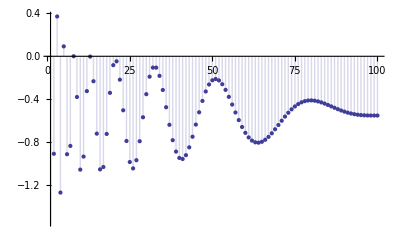

```mathematica
DiscretePlot[Im@plc5rp[100,N@Im@ZetaZero@1+.1I,j],{j,1,100}]
```

```mathematica
E^(I ArcCot[2 t]) /.t->.1
```

0.196116+0.980581 ⅈ

```mathematica
((t/I+1/2)/(t/I-1/2))^(1/2)/.t->.1
```

0.196116+0.980581 ⅈ

```mathematica
E^(-I ArcCot[2 t]) /.t->.1
```

0.196116-0.980581 ⅈ

```mathematica
((t/I-1/2)/(t/I+1/2))^(1/2)/.t->.1
```

0.196116-0.980581 ⅈ

```mathematica
plc5r[n_,x_]:=Sum[(n/j)^(1/2)(Cos[ArcCot[2 x]+x  Log[n/j]]),{j,1,n}]
plc5rpo[n_,t_]:=E^(I ArcCot[2 t])/2 n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(-I ArcCot[2 t])/2 n^(1/2-I t)HarmonicNumber[n,1/2-I t]
```

```mathematica
plc5r[10000,15.+.1I]
```

33.5606-66.4662 ⅈ

```mathematica
plc5rpo[10000,15.+.1I]
```

33.5606-66.4662 ⅈ

```mathematica
FullSimplify[D[plc5rpo[n,t],n]]
```

1/4 ⅇ^(-ⅈ ArcCot[2 t]) n^(-1/2-ⅈ t) (1-2 ⅈ t) (HarmonicNumber[n,1/2-ⅈ t]+n HurwitzZeta[3/2-ⅈ t,1+n]-n^(2 ⅈ t) (HarmonicNumber[n,1/2+ⅈ t]+n HurwitzZeta[3/2+ⅈ t,1+n]))

```mathematica
at[n_,t_]:=1/4 ⅇ^(-ⅈ ArcCot[2 t]) n^(-1/2-ⅈ t) (1-2 ⅈ t) (HarmonicNumber[n,1/2-ⅈ t]+n HurwitzZeta[3/2-ⅈ t,1+n]-n^(2 ⅈ t) (HarmonicNumber[n,1/2+ⅈ t]+n HurwitzZeta[3/2+ⅈ t,1+n]))
at2[n_,t_]:=1/4 ⅇ^(-ⅈ ArcCot[2 t]) (1-2 ⅈ t) (n^(-1/2-ⅈ t) (HarmonicNumber[n,1/2-ⅈ t]+n HurwitzZeta[3/2-ⅈ t,1+n])-n^(-1/2+ⅈ t) (HarmonicNumber[n,1/2+ⅈ t]+n HurwitzZeta[3/2+ⅈ t,1+n]))
at2a[n_,t_]:= (n^(-1/2-ⅈ t) (HarmonicNumber[n,1/2-ⅈ t]+n HurwitzZeta[3/2-ⅈ t,1+n])-n^(-1/2+ⅈ t) (HarmonicNumber[n,1/2+ⅈ t]+n HurwitzZeta[3/2+ⅈ t,1+n]))
at3[n_,t_]:={1/4 ⅇ^(-ⅈ ArcCot[2 t]), (1-2 ⅈ t), n^(-1/2-ⅈ t) (HarmonicNumber[n,1/2-ⅈ t]+n HurwitzZeta[3/2-ⅈ t,1+n]),-n^(-1/2+ⅈ t) (HarmonicNumber[n,1/2+ⅈ t]+n HurwitzZeta[3/2+ⅈ t,1+n])}
at4[n_,t_]:={1/4 ⅇ^(-ⅈ ArcCot[2 t]), (1-2 ⅈ t), {{n^(-1/2-ⅈ t) ,HarmonicNumber[n,1/2-ⅈ t],n HurwitzZeta[3/2-ⅈ t,1+n]},{-n^(-1/2+ⅈ t) ,HarmonicNumber[n,1/2+ⅈ t],n HurwitzZeta[3/2+ⅈ t,1+n]}}}
at4a[n_,t_]:={1/4 ⅇ^(-ⅈ ArcCot[2 t]), (1-2 ⅈ t), {{n^(-1/2-ⅈ t) ,HarmonicNumber[n,1/2-ⅈ t]+n HurwitzZeta[3/2-ⅈ t,1+n]},{-n^(-1/2+ⅈ t) ,HarmonicNumber[n,1/2+ⅈ t]+n HurwitzZeta[3/2+ⅈ t,1+n]}}}
at4b[n_,t_]:={1/4 ⅇ^(-ⅈ ArcCot[2 t]), (1-2 ⅈ t), {{n^(-1/2-ⅈ t) HarmonicNumber[n,1/2-ⅈ t],n^(-1/2-ⅈ t)n HurwitzZeta[3/2-ⅈ t,1+n]},{-n^(-1/2+ⅈ t)HarmonicNumber[n,1/2+ⅈ t],-n^(-1/2+ⅈ t)n HurwitzZeta[3/2+ⅈ t,1+n]}}}
```

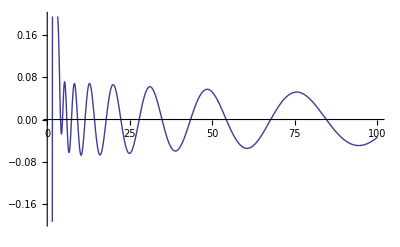

```mathematica
Plot[Re@at2[n,N@Im@ZetaZero@1+.1I],{n,1,100}]
```

```mathematica
n^(-1/2-ⅈ t) n^(2 ⅈ t)
```

n^(-1/2+ⅈ t)

```mathematica
at4a[10000,N@Im@ZetaZero@1]
```

{0.249844-0.00883794 ⅈ,1.-28.2695 ⅈ,{{-0.00189316+0.00981916 ⅈ,-0.0946389-0.490859 ⅈ},{0.00189316+0.00981916 ⅈ,-0.0946389+0.490859 ⅈ}}}

```mathematica
FullSimplify[D[plc5rpo[n,t],{n,2}]]
```

1/8 ⅇ^(-ⅈ ArcCot[2 t]) n^(-3/2-ⅈ t) (-(1+4 t^2) HarmonicNumber[n,1/2-ⅈ t]+(ⅈ+2 t) (-n^(2 ⅈ t) (ⅈ+2 t) HarmonicNumber[n,1/2+ⅈ t]+n (-2 (ⅈ+2 t) HurwitzZeta[3/2-ⅈ t,1+n]+n (3 ⅈ+2 t) HurwitzZeta[5/2-ⅈ t,1+n]-n^(2 ⅈ t) ((-2 ⅈ+4 t) HurwitzZeta[3/2+ⅈ t,1+n]+n (3 ⅈ-2 t) HurwitzZeta[5/2+ⅈ t,1+n]))))

```mathematica
E^(I ArcCot[2 t])/2 n^t HarmonicNumber[ n,t]/.n->100000/.t->N@ZetaZero@1
```

125.15+3660.23 ⅈ

```mathematica
plc5rpo[n_,t_]:=E^(I ArcCot[2 t])/2 n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(-I ArcCot[2 t])/2 n^(1/2-I t)HarmonicNumber[n,1/2-I t]
plc5rpos[n_,t_]:=(1/2-t) n^(1/2+I t)HarmonicNumber[n,1/2+I t]
plc5rpos2[n_,s_]:=Im[(s-1) n^(-1/2+s) HarmonicNumber[n,s]]
plc5rpos3[n_,s_]:=Im[(s-1) n^(-1+s) HarmonicNumber[n,s]]
plc5rpos4[n_,s_]:=Im[(s-1) n^(-1/4+s) HarmonicNumber[n,s]]
```

```mathematica
plc5rpos2[1000000000,N@ZetaZero@1]
```

0.000223489

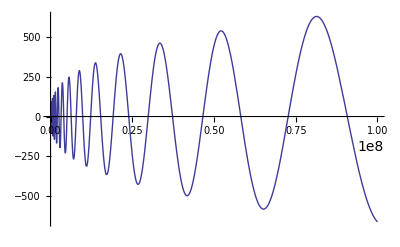

```mathematica
Plot[plc5rpos4[n,N@ZetaZero@1+.1],{n,1,100000000}]
```

```mathematica
zets[n_,t_]:=(E^(I ArcCot[2 t]) n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(-I ArcCot[2 t]) n^(1/2-I t)HarmonicNumber[n,1/2-I t])/((2^(1-(1/2+t I))Pi^-(1/2+t I) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(I ArcCot[2 t]) n^(1/2+I t)+E^(-I ArcCot[2 t])n^(1/2-I t))
z2[n_,s_]:=zets[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z2[100000000000,2.00000001]
```

1.64493+0. ⅈ

```mathematica
Zeta[.9]
```

-9.43011

```mathematica
FullSimplify[(E^(I ArcCot[2 t]) n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(-I ArcCot[2 t]) n^(1/2-I t)HarmonicNumber[n,1/2-I t])/((2^(1-(1/2+t I))Pi^-(1/2+t I) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(I ArcCot[2 t]) n^(1/2+I t)+E^(-I ArcCot[2 t])n^(1/2-I t))]
```

(2^(ⅈ t) π^(1/2+ⅈ t) (HarmonicNumber[n,1/2-ⅈ t]+ⅇ^(2 ⅈ ArcCot[2 t]) n^(2 ⅈ t) HarmonicNumber[n,1/2+ⅈ t]))/(2^(ⅈ t) π^(1/2+ⅈ t)+√2 ⅇ^(2 ⅈ ArcCot[2 t]) n^(2 ⅈ t) Cos[1/4 (π+2 ⅈ π t)] Gamma[1/2+ⅈ t])

```mathematica
zets3[n_,t_]:=(E^(1/2+I ArcCot[2 t]) n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(1/2-I ArcCot[2 t]) n^(1/2-I t)HarmonicNumber[n,1/2-I t])/((2^(1-(1/2+t I))Pi^-(1/2+t I) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(1/2+I ArcCot[2 t]) n^(1/2+I t)+E^(1/2-I ArcCot[2 t])n^(1/2-I t))
z3[n_,s_]:=zets3[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z3[100000000000,.8+I]
```

0.374874+0.886413 ⅈ

```mathematica
Zeta[.8+I]
```

0.374874-0.886413 ⅈ

```mathematica
(E^(I ArcCot[2 t]) n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(-I ArcCot[2 t]) n^(1/2-I t)HarmonicNumber[n,1/2-I t])/((2^(1-(1/2+t I))Pi^-(1/2+t I) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(I ArcCot[2 t]) n^(1/2+I t)+E^(-I ArcCot[2 t])n^(1/2-I t))
```

(ⅇ^(-ⅈ ArcCot[2 t]) n^(1/2-ⅈ t) HarmonicNumber[n,1/2-ⅈ t]+ⅇ^(ⅈ ArcCot[2 t]) n^(1/2+ⅈ t) HarmonicNumber[n,1/2+ⅈ t])/(ⅇ^(-ⅈ ArcCot[2 t]) n^(1/2-ⅈ t)+2^(1/2-ⅈ t) ⅇ^(ⅈ ArcCot[2 t]) n^(1/2+ⅈ t) π^(-1/2-ⅈ t) Cos[1/2 π (1/2+ⅈ t)] Gamma[1/2+ⅈ t])

```mathematica
zets4[n_,t_]:=(E^(1/2+I ArcCot[2 t]) n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(1/2-I ArcCot[2 t]) n^(1/2-I t)HarmonicNumber[n,1/2-I t])/((2^(1-(1/2+t I))Pi^-(1/2+t I) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(1/2+I ArcCot[2 t]) n^(1/2+I t)+E^(1/2-I ArcCot[2 t])n^(1/2-I t))
z4[n_,s_]:=zets4[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z4[100000000000,.8+I]
```

0.374874+0.886413 ⅈ

```mathematica
(E^(1/2+I ArcCot[2 t]) n^(1/2+I t)HarmonicNumber[n,1/2+I t]+E^(1/2-I ArcCot[2 t]) n^(1/2-I t)HarmonicNumber[n,1/2-I t])/((2^(1-(1/2+t I))Pi^-(1/2+t I) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(1/2+I ArcCot[2 t]) n^(1/2+I t)+E^(1/2-I ArcCot[2 t])n^(1/2-I t))
```

(ⅇ^(1/2-ⅈ ArcCot[2 t]) n^(1/2-ⅈ t) HarmonicNumber[n,1/2-ⅈ t]+ⅇ^(1/2+ⅈ ArcCot[2 t]) n^(1/2+ⅈ t) HarmonicNumber[n,1/2+ⅈ t])/(ⅇ^(1/2-ⅈ ArcCot[2 t]) n^(1/2-ⅈ t)+2^(1/2-ⅈ t) ⅇ^(1/2+ⅈ ArcCot[2 t]) n^(1/2+ⅈ t) π^(-1/2-ⅈ t) Cos[1/2 π (1/2+ⅈ t)] Gamma[1/2+ⅈ t])

```mathematica
zets5[n_,t_]:=(E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])HarmonicNumber[n,1/2+I t]+
E^(1/2-I ArcCot[2 t]) E^((1/2-I t)Log[n])HarmonicNumber[n,1/2-I t])/
((E^((1/2-t I)Log[2])E^((-1/2-t I)Log[Pi]) Cos[ Pi (1/2+t I)/2]Gamma[(1/2+t I)]) E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])+
E^(1/2-I ArcCot[2 t])E^((1/2-I t)Log[n]))
z5[n_,s_]:=zets5[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z5[100000000000000000000,.6+30I]
```

0.0222798+0.566553 ⅈ

```mathematica
Zeta[1.6+30I]
```

0.725453-0.345898 ⅈ

```mathematica
1-(1/2+t I)
```

1/2-ⅈ t

```mathematica
zets6[n_,t_]:=(E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])HarmonicNumber[n,1/2+I t]+
E^(1/2-I ArcCot[2 t]) E^((1/2-I t)Log[n])HarmonicNumber[n,1/2-I t])/
((E^((1/2-t I)Log[2])E^((-1/2-t I)Log[Pi])((1/2)(E^(I( Pi (1/2+t I)/2))+E^(-I( Pi (1/2+t I)/2))))Gamma[(1/2+t I)]) E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])+
E^(1/2-I ArcCot[2 t])E^((1/2-I t)Log[n]))
z6[n_,s_]:=zets6[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z6[100000000000000000000,.6+30I]
```

0.0222798+0.566553 ⅈ

```mathematica
zets7[n_,t_]:=Sum[(E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n/j])+
E^(1/2-I ArcCot[2 t]) E^((1/2-I t)Log[n/j]))/
((E^((1/2-t I)Log[2])E^((-1/2-t I)Log[Pi])((1/2)(E^(I( Pi (1/2+t I)/2))+E^(-I( Pi (1/2+t I)/2))))Gamma[(1/2+t I)]) E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])+
E^(1/2-I ArcCot[2 t])E^((1/2-I t)Log[n])),{j,1,n}]
z7[n_,s_]:=zets7[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z7[10000,1.6+30I]
```

0.725453+0.345898 ⅈ

```mathematica
E^(-EulerGamma (1/2+t I))/(1/2+t I) Product[ (1+(1/2+t I)/n)^-1 E^((1/2+t I)/n),{n,1,Infinity}]
```

(ⅇ^(-EulerGamma (1/2+ⅈ t)+1/2 EulerGamma (1+2 ⅈ t)) Gamma[3/2+ⅈ t])/(1/2+ⅈ t)

```mathematica
zets8[n_,t_]:=Sum[(E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n/j])+
E^(1/2-I ArcCot[2 t]) E^((1/2-I t)Log[n/j]))/
((E^((1/2-t I)Log[2])E^((-1/2-t I)Log[Pi])((1/2)(E^(I( Pi (1/2+t I)/2))+E^(-I( Pi (1/2+t I)/2))))E^(-EulerGamma (1/2+t I))/(1/2+t I) Product[ (1+(1/2+t I)/k)^-1 E^((1/2+t I)/k),{k,1,Infinity}]) E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])+
E^(1/2-I ArcCot[2 t])E^((1/2-I t)Log[n])),{j,1,n}]
z8[n_,s_]:=zets8[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z8[10000,1.6+30I]
```

0.725453+0.345898 ⅈ

```mathematica
zets9[n_,t_]:=Sum[(E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n/j])+
E^(1/2-I ArcCot[2 t]) E^((1/2-I t)Log[n/j]))/
((E^((1/2-t I)Log[2])E^((-1/2-t I)Log[Pi])((1/2)(E^(I( Pi (1/2+t I)/2))+E^(-I( Pi (1/2+t I)/2))))E^(-EulerGamma (1/2+t I))/(1/2+t I) Product[ (1+(1/2+t I)/k)^-1 E^((1/2+t I)/k),{k,1,Infinity}]) E^(1/2+I ArcCot[2 t]) E^((1/2+I t)Log[n])+
E^(1/2-I ArcCot[2 t])E^((1/2-I t)Log[n])),{j,1,n}]
z9[n_,s_]:=zets9[n,Im[s]+Re[s]I-.5I]
```

```mathematica
z9[10000,1.6+30I]
```

0.725453+0.345898 ⅈ

```mathematica
be[t_]:=(1+t/n)^-1 E^(t/n)
bo[t_]:=E^(-EulerGamma t )/t
```

```mathematica
FullSimplify[Pi^(1/2-s)bo[s/2]/bo[(1-s)/2]Product[be[s/2]/be[(1-s)/2],{n,1,Infinity}]]
```

(2 π)^-s Csc[(π s)/2] Gamma[s] Sin[π s]

```mathematica
Pi^(1/2-s)Gamma[s/2]/Gamma[(1-s)/2]/.s->.3
```

3.07154

```mathematica
(2 π)^-s Csc[(π s)/2] Gamma[s] Sin[π s]/.s->.3
```

3.07154

```mathematica
(2 π)^-s Gamma[s] Sin[π s]/Sin[Pi s/2]/.s->.3
```

3.07154

```mathematica
FullSimplify[Sin[π s]/Sin[Pi s/2]]
```

2 Cos[(π s)/2]

```mathematica
plc5e[n_,x_]:=Sum[j^(-1/2)(Cos[ArcCot[2 x]+x  Log[n/j]]),{j,1,n}]
Aa[n_,x_]:=Sum[j^(-1/2),{j,1,Floor[n]}]
plc5e2[n_,x_]:=(Cos[ArcCot[2 x]+x  Log[n/n]])Aa[n,x]-Integrate[Aa[j,x]((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,1,n}]
plc5e3[n_,x_]:=(Cos[ArcCot[2 x]+x  Log[n/n]])HarmonicNumber[Floor[n],1/2]-Integrate[HarmonicNumber[Floor[j],1/2]((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,1,n}]
plc5e3a[n_,x_]:={(Cos[ArcCot[2 x]+x  Log[n/n]])HarmonicNumber[Floor[n],1/2],-Integrate[HarmonicNumber[Floor[j],1/2]((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,1,n}]}
plc5e3b[n_,x_]:={(Cos[ArcCot[2 x]+x  Log[n/n]])HarmonicNumber[Floor[n],1/2],-Sum[HarmonicNumber[Floor[n2-1],1/2]Integrate[((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,n2-1,n2}],{n2,2,n}]}
plc5e3c0[n_,x_]:=(Cos[ArcCot[2 x]+x  Log[n/n]])HarmonicNumber[Floor[n],1/2]-Sum[HarmonicNumber[n2-1,1/2](-(√(4+1/x^2) x (2 x Cos[x Log[n/(-1+n2)]]-2 x Cos[x Log[n/n2]]-Sin[x Log[n/(-1+n2)]]+Sin[x Log[n/n2]]))/(1+4 x^2)),{n2,2,n}]
plc5e3c[n_,x_]:={(Cos[ArcCot[2 x]+x  Log[n/n]])HarmonicNumber[Floor[n],1/2],-Sum[N[HarmonicNumber[n2-1,1/2](-(√(4+1/x^2) x (2 x Cos[x Log[n/(-1+n2)]]-2 x Cos[x Log[n/n2]]-Sin[x Log[n/(-1+n2)]]+Sin[x Log[n/n2]]))/(1+4 x^2))],{n2,2,n}]}
plc5e3d[n_,x_]:={2/(√(4+1/x^2))HarmonicNumber[Floor[n],1/2],-Sum[HarmonicNumber[n2-1,1/2](-(√(4+1/x^2) x (2 x Cos[x Log[n/(-1+n2)]]-2 x Cos[x Log[n/n2]]-Sin[x Log[n/(-1+n2)]]+Sin[x Log[n/n2]]))/(1+4 x^2)),{n2,2,n}]}
plc5e3e[n_,x_]:={2/(√(4+1/x^2))HarmonicNumber[Floor[n],1/2],-Sum[HarmonicNumber[n2-1,1/2](-Cos[ArcCot[2 x]+x Log[n/(-1+n2)]]+Cos[ArcCot[2 x]+x Log[n/n2]]),{n2,2,n}]}
```

```mathematica
plc5e2[100,.3]
```

1.29208

```mathematica
plc5e3[100,.3]
```

1.29208

```mathematica
plc5e3a[100,.3]
```

{9.56427,-8.27219}

```mathematica
plc5e3a[100,.3]
```

{9.56427,-8.27219}

```mathematica
D[(Cos[ArcCot[2 x]+x  Log[n/j]]),j]
```

(x Sin[ArcCot[2 x]+x Log[n/j]])/j

```mathematica
Integrate[(x Sin[ArcCot[2 x]+x Log[n/j]])/j,j]
```

(2 x Cos[x Log[n/j]]-Sin[x Log[n/j]])/(√(4+1/x^2) x)

```mathematica
plc5e[100,.3]
```

1.29208

```mathematica
FullSimplify[Sum[j^(-1/2),{j,1,Floor[n]}]]
```

HarmonicNumber[Floor[n],1/2]

```mathematica
plc5e3[100,N@Im@ZetaZero@1]
```

Integrate::mpwc: Integrate was unable to convert Floor[j] to Piecewise because the required number 1000 of piecewise cases sought exceeds the internal limit $MaxPiecewiseCases = 100.

61.7624-∫_1^1000 (14.1347 HarmonicNumber[Floor[j],1/2] Sin[0.0353591+14.1347 Log[1000/j]])/j ⅆj

```mathematica
Integrate[((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,n,n+1}]
```

ConditionalExpression[(2 x (-1+Cos[x Log[n/(1+n)]])-Sin[x Log[n/(1+n)]])/(√(4+1/x^2) x),Re[n]>0||Re[n]≤-1||n∉Reals]

```mathematica
FullSimplify[(2 x (-1+Cos[x Log[n/(1+n)]])-Sin[x Log[n/(1+n)]])/(√(4+1/x^2) x)]
```

(2 x (-1+Cos[x Log[n/(1+n)]])-Sin[x Log[n/(1+n)]])/(√(4+1/x^2) x)

```mathematica
Integrate[((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,n-1,n}]
```

ConditionalExpression[(2 x-2 x Cos[x Log[n/(-1+n)]]+Sin[x Log[n/(-1+n)]])/(√(4+1/x^2) x),Re[n]≥1||Re[n]≤0||n∉Reals]

```mathematica
Integrate[((x Sin[ArcCot[2 x]+x Log[n/j]])/j),{j,n2-1,n2}]
```

ConditionalExpression[-(√(4+1/x^2) x (2 x Cos[x Log[n/(-1+n2)]]-2 x Cos[x Log[n/n2]]-Sin[x Log[n/(-1+n2)]]+Sin[x Log[n/n2]]))/(1+4 x^2),Re[n2]≥1||Re[n2]≤0||n2∉Reals]

```mathematica
FullSimplify[-(√(4+1/x^2) x (2 x Cos[x Log[n/(-1+n2)]]-2 x Cos[x Log[n/n2]]-Sin[x Log[n/(-1+n2)]]+Sin[x Log[n/n2]]))/(1+4 x^2)]/.n2->a
```

(√(4+1/x^2) x (-2 x Cos[x Log[n/(-1+a)]]+2 x Cos[x Log[n/a]]+Sin[x Log[n/(-1+a)]]-Sin[x Log[n/a]]))/(1+4 x^2)

```mathematica
FullSimplify[(Cos[ArcCot[2 x]])]
```

2/(√(4+1/x^2))

```mathematica
((Cos[ArcCot[2 x]+x  Log[n/j]])/.j->n2)-((Cos[ArcCot[2 x]+x  Log[n/j]])/.j->(n2-1))
```

-Cos[ArcCot[2 x]+x Log[n/(-1+n2)]]+Cos[ArcCot[2 x]+x Log[n/n2]]

```mathematica
FullSimplify[-Cos[ArcCot[2 x]+x Log[n/(-1+n2)]]+Cos[ArcCot[2 x]+x Log[n/n2]]]
```

-Cos[ArcCot[2 x]+x Log[n/(-1+n2)]]+Cos[ArcCot[2 x]+x Log[n/n2]]

```mathematica
tc[n_,t_,j_]:= j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]]/Cos[ t Log[n]  + ArcCot[ 2 t]]
tn[n_,t_]:= Sum[ N[tc[n,t,j]],{j,1,n}]
tl[t_]:= Table[ Limit[ tc[n,t,j],n->Infinity],{j,1,30}]
tl2[t_]:= Sum[ Limit[ tc[n,t,j],n->Infinity],{j,1,100}]
tco[n_,t_,j_]:= j^(-1/2) (Cos[ t Log[j]]+Tan[t Log[n]+ArcCot[2 t]]Sin[t Log[j]])
tcoa[n_,t_,j_]:= {j^(-1/2),Cos[ t Log[j]],Tan[t Log[n]+ArcCot[2 t]],Sin[t Log[j]]}
tco2[t_]:= Sum[ Limit[ tc[n,t,j],n->Infinity],{j,1,100}]
tcr[n_,t_]:=Sum[ j^(-1/2) (Cos[ t Log[j]]+I Sin[t Log[j]]),{j,1,n}]
tcs[n_,t_]:=Sum[ j^(-1/2) (Cos[ t Log[j]]+Tan[t Log[n]+ArcCot[2 t]] Sin[t Log[j]]),{j,1,n}]
tcs2[n_,t_]:=Sum[ j^(-1/2) (Cos[ t Log[j]]+I Sin[t Log[j]]+( Tan[t Log[n]+ArcCot[2 t]]-I) Sin[t Log[j]]),{j,1,n}]
tcs3[n_,t_]:=Sum[ j^(-1/2) (Cos[ t Log[j]]+I Sin[t Log[j]]),{j,1,n}]-Sum[ j^(-1/2) ((I- Tan[t Log[n]+ArcCot[2 t]]) Sin[t Log[j]]),{j,1,n}]
tcs4[n_,t_]:=Sum[ j^(-1/2+ⅈ t),{j,1,n}]-(I- Tan[t Log[n]+ArcCot[2 t]]) Sum[ j^(-1/2) Sin[t Log[j]],{j,1,n}]
tcs5[n_,t_]:=Sum[ j^(-1/2+ⅈ t),{j,1,n}]-(I- Tan[t Log[n]+ArcCot[2 t]]) Sum[ j^(-1/2) ((1/(2 I))(j^(I t)-j^(-I t))),{j,1,n}]
tcs6[n_,t_]:=Sum[ j^(-1/2+ⅈ t),{j,1,n}]-1/2 (1+ⅈ Tan[ArcCot[2 t]+t Log[n]]) Sum[ j^(I t-1/2)-j^(-I t-1/2),{j,1,n}]
```

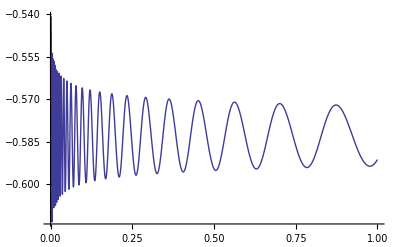

```mathematica
Plot[Re@ tc[n,14.3+.1I,2],{n,0,1000000000}]
```

```mathematica
j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]]/Cos[ t Log[n]  + ArcCot[ 2 t]]/.j->2/.t->N@Im@ZetaZero@1+.3I
```

(Cos[(9.7621+0.208694 ⅈ)-(14.1347+0.3 ⅈ) Log[n]] Sech[(0.000749512+0.0353432 ⅈ)-(0.3-14.1347 ⅈ) Log[n]])/(√2)

```mathematica
Limit[(Cos[(9.7621016365162+0.2086936658426518 ⅈ)-(14.134725141734695+0.3 ⅈ) Log[n]] Sech[(0.0007495116746682122+0.03534324346697683 ⅈ)-(0.3-14.134725141734695 ⅈ) Log[n]])/(√2),n->Infinity]
```

-0.534926-0.209121 ⅈ

```mathematica
Table[ j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]]/Cos[ t Log[n]  + ArcCot[ 2 t]]/.j->2/.t->N@Im@ZetaZero@1+.3I
```

```mathematica
Limit[j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]]/Cos[ t Log[n]  + ArcCot[ 2 t]]/.j->2,n->Infinity]
```

ⅇ^(-2 ⅈ Interval[{0,π}]+2 ⅈ Interval[{0,π}])/(√2)

```mathematica
(ⅇ^(-t Arg[j]-2 ⅈ Interval[{0,π}]) (ⅇ^(2 t Arg[j]+2 ⅈ Interval[{0,π}])+ⅇ^(2 ⅈ Interval[{0,π}])))/(2 √j)
```

(ⅇ^(-t Arg[j]+2 ⅈ Interval[{-π,0}]) (ⅇ^(2 t Arg[j]+2 ⅈ Interval[{0,π}])+ⅇ^(2 ⅈ Interval[{0,π}])))/(2 √j)

```mathematica
Limit[j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]],n->Infinity]
```

(ⅇ^(-t Arg[j]) (ⅇ^(2 t Arg[j]+2 ⅈ Interval[{0,π}])+ⅇ^(2 ⅈ Interval[{0,π}])))/(2 √j)

```mathematica
N[j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]]/Cos[ t Log[n]  + ArcCot[ 2 t]]/.j->2/.t->Im@ZetaZero@1+.01I]
```

0.707107 Cos[(9.76209+0.00695647 ⅈ)-(14.1347+0.01 ⅈ) Log[n]] Sech[(0.0000249949+0.0353591 ⅈ)-(0.01-14.1347 ⅈ) Log[n]]

```mathematica
Limit[0.7071067811865475 Cos[(9.762085766172962+0.006956466737293951 ⅈ)-(14.134725141734695+0.01 ⅈ) Log[n]] Sech[(0.000024994931694497765+0.03535911381021402 ⅈ)-(0.01-14.134725141734695 ⅈ) Log[n]],n->Infinity]
```

-0.654022-0.25568 ⅈ

```mathematica
tl[N@Im@ZetaZero@1+.1I]//TableForm
```

-0.614468-0.240217 ⅈ
-0.508982+0.0922935 ⅈ
0.319867+0.295211 ⅈ
-0.27654-0.26169 ⅈ
0.334924+0.0655546 ⅈ
-0.223487+0.216461 ⅈ
-0.125633-0.258235 ⅈ
0.250544-0.0939514 ⅈ
0.107063+0.22723 ⅈ
-0.186835+0.146183 ⅈ
-0.190053-0.120735 ⅈ
0.0270831-0.212886 ⅈ
0.189323-0.0793228 ⅈ
0.164906+0.107672 ⅈ
0.0151653+0.188857 ⅈ
-0.128068+0.130294 ⅈ
-0.17652-0.00245482 ⅈ
-0.121721-0.119965 ⅈ
-0.0112023-0.165344 ⅈ
0.0937728-0.130801 ⅈ
0.14992-0.044944 ⅈ
0.143818+0.0503971 ⅈ
0.0877786+0.119842 ⅈ
0.00799293+0.144735 ⅈ
-0.0677805+0.124306 ⅈ
-0.118851+0.0709431 ⅈ
-0.135388+0.00326279 ⅈ
-0.118112-0.060281 ⅈ
-0.0754648-0.105775 ⅈ

```mathematica
tn[100,.3I+30]
```

0.212089+0.463681 ⅈ

```mathematica
Zeta[.8+30I]
```

0.252252-0.525921 ⅈ

```mathematica
tl2[.3I+30]
```

-0.740908+0.442076 ⅈ

```mathematica
tco2[.3I+30]
```

$Aborted

```mathematica
tc[n,x,1]
```

1

```mathematica
1+-0.7409083225112658+0.4420760093125105 ⅈ
```

0.259092+0.442076 ⅈ

```mathematica
Limit[j^(-1/2) Cos[ t Log[n] - t Log[j] + ArcCot[ 2 t]]/Cos[ t Log[n]  + ArcCot[ 2 t]],n->Infinity]
```

(ⅇ^(-t Arg[j]-2 ⅈ Interval[{0,π}]) (ⅇ^(2 t Arg[j]+2 ⅈ Interval[{0,π}])+ⅇ^(2 ⅈ Interval[{0,π}])))/(2 √j)

```mathematica
Limit[j^(-1/2) Cos[ t Log[n] - t Log[j]]/Cos[ t Log[n]  ]/.j->2/.t->10+.1I,n->Infinity]
```

0.525903+0.398374 ⅈ

```mathematica
FullSimplify[tco[n,10+.1I,2]]
```

(0.565003-0.0296187 ⅈ)+(0.0391004-0.427992 ⅈ) Tanh[(0.000498704+0.0499534 ⅈ)-(0.1-10. ⅈ) Log[n]]

```mathematica
Limit[ (0.565003262515136-0.029618747630025505 ⅈ)+(0.039100442139108245-0.4279923225174692 ⅈ) Tanh[(0.0004987035366082857+0.049953421122248966 ⅈ)-(0.1-10. ⅈ) Log[n]],n->Infinity]
```

0.525903+0.398374 ⅈ

```mathematica
Limit[tco[n,x,3],n->Infinity]
```

ⅇ^(-2 ⅈ Interval[{0,π}]+2 ⅈ Interval[{0,π}])/(√3)

```mathematica
Limit[Tan[t Log[n]+ArcCot[2 t]]/.t->10+.6I,n->Infinity]
```

0.+1. ⅈ

```mathematica
tcoa[10000000000000000,10+.1I,2]
```

{1/(√2),0.799035-0.0418872 ⅈ,0.00123206+1.00028 ⅈ,0.605273+0.0552964 ⅈ}

```mathematica
tcr[100000,.45I]
```

16.1392+0. ⅈ

```mathematica
Zeta[.95+3I]
```

0.619329-0.105393 ⅈ

```mathematica
tcs4[100000,.45I+3]
```

0.619307+0.105384 ⅈ

```mathematica
tcs6[10000,.45I+3]
```

0.619129+0.105481 ⅈ

```mathematica
N[Tan[t Log[n]+ArcCot[2 t]]/.t->.2I+10]/.n->100000000000
```

-0.0000610936+1.00005 ⅈ

```mathematica
ac[n_,t_]:=(t Sin[t Log[n]]+(1/2)Cos[t Log[n]])/(t Cos[t Log[n]]-(1/2)Sin[t Log[n]])
ac2[n_,t_]:=Tan[t Log[n]+ArcCot[2 t]]
```

```mathematica
ac[100,.3I+10]
```

-0.119026+1.05256 ⅈ

```mathematica
ac2[100,.3I+10]
```

-0.119026+1.05256 ⅈ

```mathematica
Limit[ ac[n,.3I+10],n->Infinity]
```

0.+1. ⅈ

```mathematica
FullSimplify[j^(-1/2) (Cos[ t Log[j]]+I Sin[t Log[j]])]
```

j^(-1/2+ⅈ t)

```mathematica
FullSimplify[j^(-1/2) ((I- Tan[t Log[n]+ArcCot[2 t]]) Sin[t Log[j]])]
```

-(Sin[t Log[j]] (-ⅈ+Tan[ArcCot[2 t]+t Log[n]]))/(√j)

```mathematica
FullSimplify[j^(-1/2) ((j^(I t)-j^(-I t)))]
```

j^(-1/2-ⅈ t) (-1+j^(2 ⅈ t))

```mathematica
FullSimplify[(1/(2 I))(I- Tan[t Log[n]+ArcCot[2 t]])]
```

1/2 (1+ⅈ Tan[ArcCot[2 t]+t Log[n]])

```mathematica
tcs6[n_,t_]:=Sum[ j^(-1/2+ⅈ t),{j,1,n}]-1/2 (1+ⅈ Tan[ArcCot[2 t]+t Log[n]]) Sum[ j^(I t-1/2)-j^(-I t-1/2),{j,1,n}]
tcs7[n_,t_]:=HarmonicNumber[n,1/2-ⅈ t]-1/2 (HarmonicNumber[n,1/2-ⅈ t]-HarmonicNumber[n,1/2+ⅈ t]) (1+ⅈ Tan[ArcCot[2 t]+t Log[n]])
tcs8[n_,s_]:=(n s (HarmonicNumber[n,1-s]-HarmonicNumber[n,s]))/(n^(2 s) (-1+s)+n s)+HarmonicNumber[n,s]
tcs9[n_,s_]:=(n s HarmonicNumber[n,1-s])/(n^(2 s) (-1+s)+n s)-(n s HarmonicNumber[n,s])/(n^(2 s) (-1+s)+n s)+HarmonicNumber[n,s]
tcs10[n_,s_]:=HarmonicNumber[n,1-s]/(n^(2 s-1) (-1+s)/s+1)-HarmonicNumber[n,s]/(n^(2 s-1) (-1+s)/s+ 1)+HarmonicNumber[n,s]
tcs11[n_,s_]:={HarmonicNumber[n,1-s]/(n^(2 s-1) (-1+s)/s+1),-HarmonicNumber[n,s]/(n^(2 s-1) (-1+s)/s+ 1),HarmonicNumber[n,s]}
```

```mathematica
FullSimplify[Sum[ j^(-1/2+ⅈ t),{j,1,n}]-1/2 (1+ⅈ Tan[ArcCot[2 t]+t Log[n]]) Sum[ j^(I t-1/2)-j^(-I t-1/2),{j,1,n}]]
```

HarmonicNumber[n,1/2-ⅈ t]-1/2 (HarmonicNumber[n,1/2-ⅈ t]-HarmonicNumber[n,1/2+ⅈ t]) (1+ⅈ Tan[ArcCot[2 t]+t Log[n]])

```mathematica
tcs7[10000,.45I+3]
```

0.619129+0.105481 ⅈ

```mathematica
tcs6[10000,.45I+3]
```

0.619129+0.105481 ⅈ

```mathematica
FullSimplify[tcs7[n,(t-1/2) I]/.t->s]
```

(n s (HarmonicNumber[n,1-s]-HarmonicNumber[n,s]))/(n^(2 s) (-1+s)+n s)+HarmonicNumber[n,s]

```mathematica
tcs11[1000000000000000000000,.7+3I]
```

{-400118.-527131. ⅈ,-0.00235389+0.00130609 ⅈ,400119.+527131. ⅈ}

```mathematica
Zeta[.7+3I]
```

0.571252-0.0923229 ⅈ

```mathematica
FullSimplify[(n s HarmonicNumber[n,s])/(n^(2 s) (-1+s)+n s)]
```

(n s HarmonicNumber[n,s])/(n^(2 s) (-1+s)+n s)

```mathematica
FullSimplify[HarmonicNumber[n,s]/(n^(2 s-1) (-1+s)/s+ 1)+HarmonicNumber[n,s]]
```

(1+(n s)/(n^(2 s) (-1+s)+n s)) HarmonicNumber[n,s]

```mathematica
tcs10[1000000000000000000000,.7+3I]
```

0.571252-0.0923229 ⅈ

```mathematica
zz[n_,x_]:=Sum[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
zza[n_,s_]:=Sum[(Cos[ArcCot[I(2s-1)]+I( s-1/2)  Log[n/j]]/j^(1/2))/Cos[ArcCot[I(2s-1)]+I( s-1/2)  Log[n]],{j,1,n}]
zzb[n_,s_]:=Sum[(Cosh[ArcCoth[1-2s]+( s-1/2)  Log[n/j]]/j^(1/2))/Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[n]],{j,1,n}]
zz2[n_,x_]:=Sum[(Cos[ArcCot[2 x]+x  Log[n/j]+x Log[Pi]+Log[ Gamma[1/2-x/2]]-Log[Gamma[1/4+x/2]]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]+x Log[Pi]+Log[ Gamma[1/2-x/2]]-Log[Gamma[1/4+x/2]]],{j,1,n}]
```

```mathematica
zzb[10000,2.]
```

1.64493

```mathematica
zz[10000,.2I+1]
```

0.295264+0.801349 ⅈ

```mathematica
Zeta[.7+1I]
```

0.284305-0.841353 ⅈ

```mathematica
((.2I+1)+1/2I)/I
```

0.7-1. ⅈ

```mathematica
-(.2I+1)I+1/2
```

0.7-1. ⅈ

```mathematica
a/I
```

-ⅈ a

```mathematica
-(.7+I)I+1/2
```

1.5-0.7 ⅈ

```mathematica
-(s-1/2)/I
```

-1.+0.2 ⅈ

```mathematica
Expand[-(s-1/2)/I]
```

-ⅈ/2+ⅈ s

```mathematica
FullSimplify[(Cos[ArcCot[2 (I s-I/2)]+(I s-I/2)  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 (I s-I/2)]+(I s-I/2)  Log[n]]]
```

(Cosh[ArcCoth[1-2 s]+1/2 (-1+2 s) Log[n/j]] Sech[ArcCoth[1-2 s]-Log[n]/2+s Log[n]])/(√j)

```mathematica
ArcCot[I x ]
```

-ⅈ ArcCoth[x]

```mathematica
Cos[-I ArcCoth[(2s-1)]+I( s-1/2)  Log[n/j]]
```

Cosh[ArcCoth[1-2 s]+(-1/2+s) Log[n/j]]

```mathematica
Cos[-I ArcCoth[(2s-1)]+I( s-1/2)  Log[n]]
```

Cosh[ArcCoth[1-2 s]+(-1/2+s) Log[n]]

```mathematica
zzb[n_,s_]:=Sum[(Cosh[ArcCoth[1-2s]+( s-1/2)  Log[n/j]]/j^(1/2))/Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[n]],{j,1,n}]
zzc[n_,s_]:=Sum[(Cosh[ArcCoth[1-2s]+( s-1/2)  Log[n/j]]/j^(1/2))/Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[n]+(s-1/2) Log[Pi]+Log[Gamma[1/4-(s-1/2)/2]]-Log[Gamma[1/4+(s-1/2)/2]]],{j,1,n}]
zzd[n_,s_]:=Sum[(Cosh[ArcCoth[1-2s]+( s-1/2)  Log[n/j]]/j^(1/2))/Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[Pi n]+Log[Gamma[(1-s)/2]]-Log[Gamma[s/2]]],{j,1,n}]
```

```mathematica
zzd[10000,.2+3I]
```

0.476013-0.0545908 ⅈ

```mathematica
Zeta[.2+3I]
```

0.475964-0.0546585 ⅈ

```mathematica
FullSimplify[Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[n]+(s-1/2) Log[Pi]+Log[Gamma[1/4-(s-1/2)/2]]-Log[Gamma[1/4+(s-1/2)/2]]]]
```

Cosh[ArcCoth[1-2 s]+(-1/2+s) Log[n π]+Log[Gamma[(1-s)/2]]-Log[Gamma[s/2]]]

```mathematica
FullSimplify[(Cosh[ArcCoth[1-2s]+( s-1/2)  Log[n/j]]/j^(1/2))/Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[Pi n]+Log[Gamma[(1-s)/2]]-Log[Gamma[s/2]]]]
```

(Cosh[ArcCoth[1-2 s]+(-1/2+s) Log[n/j]] Sech[ArcCoth[1-2 s]+(-1/2+s) Log[n π]+Log[Gamma[(1-s)/2]]-Log[Gamma[s/2]]])/(√j)

```mathematica
FullSimplify[(Cosh[ArcCoth[1-2s]+( s-1/2)  Log[n/j]]/j^(1/2))/Cosh[ ArcCoth[1-2s]+( s-1/2)  Log[ n]]]
```

(Cosh[ArcCoth[1-2 s]+(-1/2+s) Log[n/j]] Sech[ArcCoth[1-2 s]+(-1/2+s) Log[n]])/(√j)

```mathematica
j=1+x^2
j-1=x^2
sqrt(j-1)=x
```

```mathematica
FullSimplify[Sin[ArcCot[(j-1)^(1/2)]]]/.j->3
```

1/(√3)

```mathematica
zz[n_,x_]:=Sum[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
zzo[n_,x_]:=Sum[Sin[ArcCot[(j-1)^(1/2)]]Cos[ArcCot[2 x]+x  Log[n/j]]/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
zzo2[n_,x_]:=(1/2)Sum[(Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n/j]]+Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n/j]])/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
zzo3[n_,x_]:=(1/2)Sum[(Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n/j]]+Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n/j]]) Sec[ArcCot[2 x]+x  Log[n]],{j,1,n}]
zzo4[n_,x_]:={(1/2)Sum[(Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n]-x Log[j]]) Sec[ArcCot[2 x]+x  Log[n]],{j,1,n}],(1/2)Sum[(Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n]+x Log[j]]) Sec[ArcCot[2 x]+x  Log[n]],{j,1,n}]}
zzo5[n_,x_]:=(1/2)Sec[ArcCot[2 x]+x  Log[n]](Sum[Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n]-x Log[j]] ,{j,1,n}]+Sum[Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n]+x Log[j]],{j,1,n}])
zzo5a[n_,x_]:={Sum[Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n]-x Log[j]] ,{j,1,n}],Sum[Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n]+x Log[j]],{j,1,n}]}
zzo5b[n_,x_]:={Sum[Sin[Pi-ArcTan[(j-1)^(1/2)]-ArcTan[2 x]+x  Log[n]-x Log[j]] ,{j,1,n}],Sum[Sin[-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]],{j,1,n}]}
zzo5c[n_,x_]:={-Sum[Sin[-ArcTan[(j-1)^(1/2)]-ArcTan[2 x]+x  Log[n]-x Log[j]] ,{j,1,n}],Sum[Sin[-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]],{j,1,n}]}
zzo5d[n_,x_]:={Sum[Sin[ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]] ,{j,1,n}],Sum[Sin[-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]],{j,1,n}]}
zzo5da[n_,x_]:=(1/2)Sec[Pi/2-ArcTan[2 x]+x  Log[n]](Sum[Sin[ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]] ,{j,1,n}]+Sum[Sin[-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]],{j,1,n}])
zzo5e[n_,x_]:={Sum[Sin[ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]] ,{j,1,n}],Sum[Sin[-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]],{j,1,n}]}
zzo5f[n_,x_]:=Sum[Sin[ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]]+Sin[-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]],{j,1,n}]
```

```mathematica
zzo5f[10000,N@Im@ZetaZero@1]
```

0.00999375

```mathematica
Zeta[.8+30I]
```

0.252252-0.525921 ⅈ

```mathematica
{(1/2)Sum[(Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n]-x Log[j]]) Sec[ArcCot[2 x]+x  Log[n]],{j,1,n}],(1/2)Sum[(Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n]+x Log[j]]) Sec[ArcCot[2 x]+x  Log[n]],{j,1,n}]}
```

{1/2 ∑_(j=1)^n Sec[ArcCot[2 x]+x Log[n]] Sin[ArcCot[√(-1+j)]+ArcCot[2 x]-x Log[j]+x Log[n]],1/2 ∑_(j=1)^n Sec[ArcCot[2 x]+x Log[n]] Sin[ArcCot[√(-1+j)]-ArcCot[2 x]+x Log[j]-x Log[n]]}

```mathematica
N@ArcCot[(j-1)^(1/2)]/.j->1
```

1.5708

```mathematica
{Sum[Sin[ArcCot[(j-1)^(1/2)]+ArcCot[2 x]+x  Log[n]-x Log[j]] ,{j,1,n}],Sum[Sin[ArcCot[(j-1)^(1/2)]-ArcCot[2 x]-x  Log[n]+x Log[j]],{j,1,n}]}
```

{∑_(j=1)^n Sin[ArcCot[√(-1+j)]+ArcCot[2 x]-x Log[j]+x Log[n]],∑_(j=1)^n Sin[ArcCot[√(-1+j)]-ArcCot[2 x]+x Log[j]-x Log[n]]}

```mathematica
ArcTan[(j-1)^(1/2)]
```

ArcTan[√(-1+j)]

```mathematica
ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]+-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]
```

```mathematica
Expand[(2 ArcTan[2 x]+2 x Log[j]-2 x Log[n])/2]
```

ArcTan[2 x]+x Log[j]-x Log[n]

```mathematica
(ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]-(-ArcTan[(j-1)^(1/2)]+ArcTan[2 x]-x  Log[n]+x Log[j]))/2
```

```mathematica
Cos[ArcTan[√(-1+j)]]
```

1/(√j)

```mathematica
Sin[ArcCot[(j-1)^(1/2)]]/.j->3
```

1/(√3)

```mathematica
Sin[Pi/2-ArcTan[(j-1)^(1/2)]]/.j->3
```

1/(√3)

```mathematica
Cos[ArcTan[(j-1)^(1/2)]]/.j->3
```

1/(√3)

```mathematica
ach[n_,x_,b_]:= Sum[b^(-j/2)Cos[ x Log[n]-j Log[b]+ArcCot[2 x]],{j,1,23}]
```

```mathematica
ach[10000000,N@Im@ZetaZero@2,5]
```

-0.311633

```mathematica
Log[2.,10000000]
```

23.2535

```mathematica
zt[n_,x_]:=Sum[(Sin[ArcTan[2 x]-x  Log[n/j]]/j^(1/2)),{j,1,n}]
ztz[n_,x_]:=Sum[(Sin[ArcTan[2 x]-x  Log[n/j]]/j^(1/2))/Sin[ArcTan[2 x]-x  Log[n]],{j,1,n}]
ztz2[n_,x_]:=Sum[((Sin[ArcTan[2 x]-x  Log[n]]Cos[x Log[j]]+Cos[ArcTan[2 x]-x  Log[n]]Sin[x Log[j]])/j^(1/2))/Sin[ArcTan[2 x]-x  Log[n]],{j,1,n}]
ztz3[n_,x_]:=Sum[Cos[x Log[j]]/j^(1/2),{j,1,n}]+Sum[((Cos[ArcTan[2 x]-x  Log[n]]Sin[x Log[j]])/j^(1/2))/Sin[ArcTan[2 x]-x  Log[n]],{j,1,n}]
ztz4[n_,x_]:=Sum[(Sin[ArcSin[2 x/(4x^2+1)^(1/2)]-x  Log[n/j]]/j^(1/2))/Sin[ArcSin[2 x/(4x^2+1)^(1/2)]-x  Log[n]],{j,1,n}]
```

```mathematica
ztz4[10000,N@Im@ZetaZero@1]
```

-0.0323453

```mathematica
N@ArcTan[140000]
```

1.57079

```mathematica
Sin[ArcSin[2 x/(4x^2+1)^(1/2)]]
```

(2 x)/(√(1+4 x^2))

```mathematica
Tan[t Log[n] +Pi/2-ArcTan[2 t]]
```

Cot[ArcTan[2 t]-t Log[n]]

```mathematica
Tan[ArcCot[2t]]
```

1/(2 t)

```mathematica
ezt[n_,x_]:=Sum[j^(-1/2)(Cos[x Log[j]]+Tan[x Log[n]+ArcCot[2 x]]Sin[x Log[j]]),{j,1,n}]
ezt2[n_,x_]:=Sum[j^(-1/2)(Cos[x Log[j]]+(Sin[(x Log[n]+ArcCot[2 x]) 2]/(1+Cos[(x Log[n]+ArcCot[2 x]) 2]))Sin[x Log[j]]),{j,1,n}]
ezt3[n_,x_]:=Sum[j^(-1/2)((1+Cos[(x Log[n]+ArcCot[2 x]) 2])Cos[x Log[j]]+(Sin[(x Log[n]+ArcCot[2 x]) 2])Sin[x Log[j]]),{j,1,n}]
ezt4[n_,x_]:=Sum[j^(-1/2)(Cos[x Log[j]]+(Cos[(x Log[n]+ArcCot[2 x]) 2])Cos[x Log[j]]+(Sin[(x Log[n]+ArcCot[2 x]) 2])Sin[x Log[j]]),{j,1,n}]
ezt5[n_,x_]:=Sum[j^(-1/2)(Cos[x Log[j]]+Cos[2(x Log[n]+ArcCot[2 x]) +x Log[j]]/2+Cos[2(x Log[n]+ArcCot[2 x]) -x Log[j]]/2+Cos[2(x Log[n]+ArcCot[2 x]) -x Log[j]]/2-Cos[2(x Log[n]+ArcCot[2 x]) +x Log[j]]/2),{j,1,n}]
ezt6[n_,x_]:=Sum[j^(-1/2)(Cos[x Log[j]]+Cos[x Log[j]-2 ArcCot[2 x]-2x Log[n]]),{j,1,n}]
ezt6a[n_,x_]:={Sum[j^(-1/2)Cos[x Log[j]],{j,1,n}],Sum[j^(-1/2)(Cos[x Log[j]-2 (ArcCot[2 x]+x Log[n])]),{j,1,n}]}
ezt7[n_,x_]:=Sum[j^(-1/2)(Cos[x Log[j]]+Cos[x Log[j/n^2]-2 ArcCot[2 x]]),{j,1,n}]
```

```mathematica
ezt7[10000,N@Im@ZetaZero@1]
```

-0.00154389

```mathematica
Zeta[.8+30I]
```

0.252252-0.525921 ⅈ

```mathematica
Tan[13.7]
```

2.13984

```mathematica
Sin[13.7 2]/(1+Cos[13.7 2])
```

2.13984

```mathematica
Cos[2(x Log[n]+ArcCot[2 x]) +x Log[j]]/2+Cos[2(x Log[n]+ArcCot[2 x]) -x Log[j]]/2+Cos[2(x Log[n]+ArcCot[2 x]) -x Log[j]]/2-Cos[2(x Log[n]+ArcCot[2 x]) +x Log[j]]/2
```

Cos[x Log[j]-2 (ArcCot[2 x]+x Log[n])]

```mathematica
Sum[j^(-1/2)Cos[14. Log[j]],{j,1,Infinity}]
```

$Aborted

```mathematica
Sin[N@Im@ZetaZero@1 Log[600000]]
```

-0.423671

```mathematica
ap[n_,x_]:=Tan[x Log[n]+ArcCot[2 x]]
```

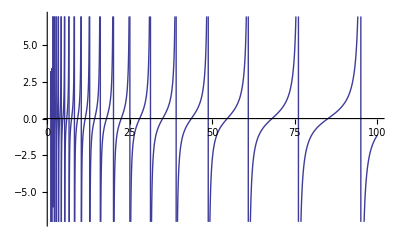

```mathematica
Plot[ap[n,N@Im@ZetaZero@1],{n,1,100}]
```

```mathematica
ext[n_,x_]:=Sum[j^(-1/2)(((1/2)(j^(I x )+ j^(-I x )))+Tan[x Log[n]+ArcCot[2 x]]Sin[x Log[j]]),{j,1,n}]
ext2[n_,x_]:=Sum[j^(-1/2)(((1/2)(j^(I x )+ j^(-I x )))+Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(j^(I x)-j^(-I x)))),{j,1,n}]
ext3[n_,x_]:=Sum[(((1/2)(j^(-1/2+I x )+ j^(-1/2-I x )))+Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(j^(-1/2+I x)-j^(-1/2-I x)))),{j,1,n}]
ext4[n_,x_]:=(1/2)(HarmonicNumber[n,1/2-I x]+HarmonicNumber[n,1/2+I x])+Sum[(Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(j^(-1/2+I x)-j^(-1/2-I x)))),{j,1,n}]
ext5[n_,x_]:=(1/2)(HarmonicNumber[n,1/2-I x]+HarmonicNumber[n,1/2+I x])+(Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(HarmonicNumber[n,(1/2-I x)]-HarmonicNumber[n,(1/2+I x)])))
ext6[n_,x_]:=1/2 (HarmonicNumber[n,1/2-ⅈ x] (1-ⅈ Tan[ArcCot[2 x]+x Log[n]])+HarmonicNumber[n,1/2+ⅈ x] (1+ⅈ Tan[ArcCot[2 x]+x Log[n]]))
ext6a[n_,x_]:={1/2 HarmonicNumber[n,1/2-ⅈ x],+1/2 HarmonicNumber[n,1/2+ⅈ x],-1/2 ⅈ HarmonicNumber[n,1/2-ⅈ x] Tan[ArcCot[2 x]+x Log[n]],+1/2 ⅈ HarmonicNumber[n,1/2+ⅈ x] Tan[ArcCot[2 x]+x Log[n]]}
```

```mathematica
ext6a[100000000000, N@Im@ZetaZero@1]
```

{-1068.46-11128. ⅈ,-1068.46+11128. ⅈ,1068.46-102.589 ⅈ,1068.46+102.589 ⅈ}

```mathematica
Zeta[.4+N@Im@ZetaZero@1I]
```

-0.0814815-0.013674 ⅈ

```mathematica
FullSimplify[(1/2)(HarmonicNumber[n,1/2-I x]+HarmonicNumber[n,1/2+I x])+(Tan[x Log[n]+ArcCot[2 x]]((1/(2 I))(HarmonicNumber[n,(1/2-I x)]-HarmonicNumber[n,(1/2+I x)])))]
```

1/2 (HarmonicNumber[n,1/2-ⅈ x] (1-ⅈ Tan[ArcCot[2 x]+x Log[n]])+HarmonicNumber[n,1/2+ⅈ x] (1+ⅈ Tan[ArcCot[2 x]+x Log[n]]))

```mathematica
Expand[1/2 (HarmonicNumber[n,1/2-ⅈ x] (1-ⅈ Tan[ArcCot[2 x]+x Log[n]])+HarmonicNumber[n,1/2+ⅈ x] (1+ⅈ Tan[ArcCot[2 x]+x Log[n]]))]
```

1/2 HarmonicNumber[n,1/2-ⅈ x]+1/2 HarmonicNumber[n,1/2+ⅈ x]-1/2 ⅈ HarmonicNumber[n,1/2-ⅈ x] Tan[ArcCot[2 x]+x Log[n]]+1/2 ⅈ HarmonicNumber[n,1/2+ⅈ x] Tan[ArcCot[2 x]+x Log[n]]

```mathematica
ext6[100000000000000000000, 10.+.1I]
```

1.50989+0.115354 ⅈ

```mathematica
Zeta[.6+10I]
```

1.50992-0.115339 ⅈ

```mathematica
xx[n_,x_]:=Sum[(Cos[ArcCot[2 x]+x  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x]+x  Log[n]],{j,1,n}]
xx2[n_,x_]:=Sum[(Cos[ArcCot[2 x/I]+x/I  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x/I]+x/I  Log[n]],{j,1,n}]
xx3[n_,x_]:=Sum[(Cosh[ArcCoth[2 x]-x  Log[n/j]]/j^(1/2))Sech[ArcCoth[2 x]-x  Log[n]],{j,1,n}]
xx4[n_,x_]:=Sum[N[(Cosh[x  Log[n/j]-ArcCoth[2 x]]/j^(1/2))Sech[x  Log[n]-ArcCoth[2 x]]],{j,1,n}]
xx4a[n_,x_]:=Sum[N[(Cosh[x  Log[n/j]-((1/2)Log[(2x+1)/(2x-1)])]/j^(1/2))Sech[x  Log[n]-((1/2)Log[(2x+1)/(2x-1)])]],{j,1,n}]
xx5[n_,x_]:=Sum[(Cosh[x  Log[n/j]-ArcCoth[2 x]]/j^(1/2)),{j,1,n}]
xx6[n_,x_]:=Sum[(Cosh[x  Log[n/j]-((1/2)Log[(2x+1)/(2x-1)])]/j^(1/2)),{j,1,n}]
xx7[n_,x_]:=Sum[(Cosh[x  Log[n/j]-ArcCoth[2 x]](n/j)^(1/2)),{j,1,n}]
```

```mathematica
xx7[1000,N@ZetaZero@1-1/2+.1]
```

-1.09019-1.29846 ⅈ

```mathematica
Zeta[.77+190I]
```

1.75954+0.976522 ⅈ

```mathematica
ArcCot[2x I]
```

-ⅈ ArcCoth[2 x]

```mathematica
Cos[I x]
```

Cosh[x]

```mathematica
(.3I+30)/I
```

0.3-30. ⅈ

```mathematica
(Cos[ArcCot[2 x/I]+x/I  Log[n/j]]/j^(1/2))/Cos[ArcCot[2 x/I]+x/I  Log[n]]
```

(Cosh[ArcCoth[2 x]-x Log[n/j]] Sech[ArcCoth[2 x]-x Log[n]])/(√j)

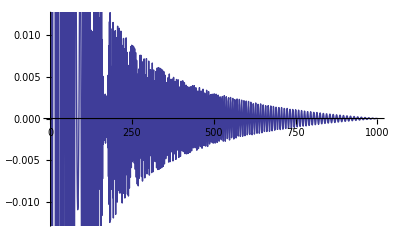

```mathematica
DiscretePlot[Im[ Cosh[(sss=.1+530 I) Log[1000/j]+ArcCoth[2 (sss)]]/j^(1/2)],{j,1,1000}]
```

```mathematica
x  Log[n/j]-((1/2)Log[(2x+1)/(2x-1)])
```

```mathematica
Log[(n/j)^x/(((2x+1)/(2x-1))^(1/2))]
```

Log[(n/j)^x/(√((1+2 x)/(-1+2 x)))]

```mathematica
Log[(n/j)^x (((2x+1)/(2x-1))^(-1/2))]
```

Log[(n/j)^x/(√((1+2 x)/(-1+2 x)))]

```mathematica
xx8[n_,x_]:=Sum[(E^(x  Log[n/j]-ArcCoth[2 x])+E^(-(x  Log[n/j]-ArcCoth[2 x])))/2((n/j)^(1/2)),{j,1,n}]
xx9[n_,x_]:=Sum[(E^(x  Log[n/j])E^-ArcCoth[2 x]+E^(-x  Log[n/j])E^ArcCoth[2 x])/2((n/j)^(1/2)),{j,1,n}]
xx10[n_,x_]:=Sum[((n/j)^x E^-ArcCoth[2 x]+(n/j)^-x E^ArcCoth[2 x])/2((n/j)^(1/2)),{j,1,n}]
xx11[n_,x_]:=Sum[((n/j)^(x+1/2) E^-ArcCoth[2 x]+(n/j)^(-x+1/2) E^ArcCoth[2 x])/2,{j,1,n}]
xx12[n_,x_]:=E^-ArcCoth[2 x]/2Sum[((n/j)^(x+1/2) ),{j,1,n}]+E^ArcCoth[2 x]/2Sum[((n/j)^(-x+1/2) ),{j,1,n}]
xx13[n_,x_]:=E^-ArcCoth[2 x]/2n^(x+1/2)Sum[j^(-x-1/2) ,{j,1,n}]+E^ArcCoth[2 x]/2n^(-x+1/2) Sum[j^(x-1/2) ,{j,1,n}]
xx14[n_,x_]:=E^-ArcCoth[2 x]/2n^(x+1/2)HarmonicNumber[n,x+1/2]+E^ArcCoth[2 x]/2n^(-x+1/2) HarmonicNumber[n,-x+1/2]
xx15[n_,x_]:=E^-ArcCoth[2 x]/2n^(x+1/2)(Zeta[x+1/2]-Zeta[x+1/2,n+1])+E^ArcCoth[2 x]/2n^(-x+1/2) (Zeta[-x+1/2]-Zeta[-x+1/2,n+1])
xx16[n_,x_]:=E^-ArcCoth[2 x]/2n^(1/2+x)(Zeta[1/2+x])+E^ArcCoth[2 x]/2n^(1/2-x) (Zeta[1/2-x])
```

```mathematica
xx14[10000000,.2+10I]
```

-35099.5-47114.8 ⅈ

```mathematica
xx16[10000000,.2+10I]
```

-35100.-47114.8 ⅈ

```mathematica
Plot[{-100,Abs[xx14[n,140000 ⅈ+.01]]},{n,1,10000000000000000}]
```

-Graphics-

```mathematica
Plot[{-100,Abs[xx16[n,140000 ⅈ+.01]]},{n,1,10000000000000000}]
```

-Graphics-